# -Graphics-

# High-Performance Code

## In the Wolfram Language

## Introduction

This training session provides advice for writing Wolfram Language code that executes in the least time. The advice should be balanced against the competing aims of writing code in the least time and writing code that is easy to read and maintain.

#### Contents

General advice

Built-in functions

Floating-point numbers

Lists vs. associations

Special data structures

Lists

DataStructure

Anticipating usage

Parallelization

Code compilation

FunctionCompile

Compilation types

Caching and memoization

Additional tips

Summary

## General Advice

### Built-in Functions

Generally, it is not a good idea to try and implement functionality that already exists in the Wolfram Language unless you have a very specialized algorithm.

Built-in functions are highly optimized.

Built-in functions often implement multiple algorithms and switch automatically to the most appropriate.

There is some overhead of passing data between functions.

#### Example: Functional constructs vs. indexing

In many languages, the standard way to handle vectors is to iterate through them with an index. This is rarely the fastest way in the Wolfram Language:

```mathematica
data=RandomReal[1,{10^6}];
```

```mathematica
(temp=0;Do[temp=temp+data[[i]],{i,1,Length[data]}];temp)//AbsoluteTiming
```

If there is a built-in function for the same task, it will almost always be faster:

```mathematica
Total[data]//AbsoluteTiming
```

Even when there is no single function, handling the vector as a whole rather than indexing its elements is usually faster:

```mathematica
Table[Sin[data[[i]]],{i,1,Length[data]}];//AbsoluteTiming
```

```mathematica
Map[Sin,data];//AbsoluteTiming
```

```mathematica
Sin[data];//AbsoluteTiming
```

#### Example: Random generators

Generating data one element at a time requires many calls to RandomReal:

```mathematica
Table[RandomReal[1],10^7];//AbsoluteTiming
```

Making a single call with the dimensions of the data required is faster:

```mathematica
RandomReal[1,10^7];//AbsoluteTiming
```

#### Example: Level specifications

Generally, level specifications in functions allow you to avoid more complicated elementwise application of functions. This example takes a list of 2×2 matrices and makes a list of length-4 vectors:

```mathematica
data=RandomReal[1,{10^5,2,2}];

MatrixForm/@data[[1;;2]]
```

The simplest way is to use Map and apply Flatten across the list:

```mathematica
Map[Flatten,data];//AbsoluteTiming
```

However, a single call to Flatten can achieve the same result, using the specification that only levels 2 and 3 be flattened. This is faster:

```mathematica
Flatten[data,{{1},{2,3}}];//AbsoluteTiming
```

### Floating-Point Numbers

The Wolfram Language handles numbers as accurately as possible:

```mathematica
1/3
```

```mathematica
N[%]
```

If numbers contain a decimal point and have 16 or fewer specified digits, the Wolfram Language will represent them as machine-precision reals and compute accordingly:

```mathematica
1/3.
```

If you want the most accurate results, you should use exact or high-precision numbers from the start.

If you want the fastest results, you should use machine numbers from the start.

If you must use exact numbers, convert to reals using N as early as you can in the calculation.

#### Example: Matrix operations

This matrix contains exact rational numbers:

```mathematica
matrix=Table[1/(1+Abs[i-j]),{i,120},{j,120}];

matrix//Short
```

Computing the determinant exactly and then numericalizing the result generates a very large intermediate rational result:

```mathematica
N[Det[matrix]];//AbsoluteTiming
```

By numericalizing at the start, all operations can be performed at machine precision:

```mathematica
Det[N[matrix]]//AbsoluteTiming
```

#### Example: Numeric functions

Usually numerical computation is faster, though less accurate, than symbolic computation:

```mathematica
Integrate[1/(1+x^21),{x,0,1}]//AbsoluteTiming
```

```mathematica
N[%]
```

NIntegrate gives a numerical approximation of the integral:

```mathematica
NIntegrate[1/(1+x^21),{x,0,1}]//AbsoluteTiming
```

### Lists vs. Associations

The two basic structures for data in the Wolfram Language are List (indexed by position) and Association (indexed by key or position). While one might choose between them based on problem conceptualization, they have different performance characteristics.

Lists require less data (since they have no keys).

Lists are immutable structures that are copied when modified.

Associations are based around hash tables.

#### Example: Accumulating data

AppendTo is O(n) for List (as a fresh copy is required) but O(1) for Association:

```mathematica
(data={};Do[AppendTo[data,RandomReal[]], 50000];Take[data,3])//AbsoluteTiming
```

```mathematica
ByteCount[data]
```

```mathematica
(index=0;data=<||>;Do[AppendTo[data,(index++)->RandomReal[]], 50000];Take[data,3])//AbsoluteTiming
```

```mathematica
ByteCount[data]
```

However, this simple example would be best done directly:

```mathematica
(data=RandomReal[1,{50000}];Take[data,3])//AbsoluteTiming
```

```mathematica
ByteCount[data]
```

## Special Data Structures

### Lists

There are some special optimizations to make list processing faster.

#### Packed arrays

Notice in the last example the list generated by RandomReal was smaller than the list generated by AppendTo. This is because of some hidden optimization for List. Where List can identify in advance that all values will be the same (e.g. all machine reals), it can used as an optimized representation:

```mathematica
data=RandomReal[1,10^6];
ByteCount[data]
```

This special structure is invisible:

```mathematica
Take[data,3]
```

And conversion to a more general structure is automatic. For example, if you append any element that is not a machine real, then the whole object must be represented in a more general way:

```mathematica
data2=Append[data,1(*Not a machine real*)];
ByteCount[data2]
```

The object behaves in the same way, but more data must be processed to achieve the same results:

```mathematica
Take[data2,3]
```

You can check whether the optimized format is used:

```mathematica
Developer`PackedArrayQ[data]
```

```mathematica
Developer`PackedArrayQ[data2]
```

If your data is not packed, you can manually covert it, but the contents must be the same types:

```mathematica
data3=Developer`ToPackedArray[N@data2];
```

```mathematica
Developer`PackedArrayQ[data3]
```

#### SparseArray

An even more optimized equivalent of List is SparseArray. If most elements of a list or array are identical (typically all zero), then it is only necessary to store the nonzero elements.

For example, there are a billion elements in this list, but only the fifth element is nonzero:

```mathematica
sparseData=SparseArray[{5->17},10^9]
```

```mathematica
ByteCount[sparseData]
```

For supported operations, SparseArray is typically proportionately faster than the dense representation:

```mathematica
Total[sparseData]//AbsoluteTiming
```

```mathematica
data=Normal[sparseData];

Total[data]//AbsoluteTiming
```

Unpacking can lead to memory errors:

```mathematica
largeSparseData=SparseArray[{{i_,i_}->i},{100000,100000}]
```

```mathematica
Normal[largeSparseData]
```

For other operations, SparseArray is usually converted automatically to the dense representation.

### DataStructure

Data science provides many data structures that are optimized for certain operations with certain prior assumptions about the usage pattern and contents. The Wolfram Language supports many of these through CreateDataStructure.

DataStructure typically supports only a small set of operations for each type.

These operations are typically faster than the equivalent using List or Association data.

The currently supported set of available special data structures is given by $DataStructures:

```mathematica
$DataStructures
```

#### Example: Queues

All structures have the same interface. You start by creating the data structure:

```mathematica
queue=CreateDataStructure["Queue"]
```

In the case of "Queue", there are nine supported operations: Copy, DropAll, Elements, EmptyQ, Length, Peek, Pop, Push and Visualization. Performance complexity is documented for each data structure. In the case of "Queue" these are:

```mathematica
CellPrint[
ExpressionCell[
Grid[
{
{"Operation", "Action", "Time"},
{Style["ds[\"Copy\"]", "CodeText"], "Return a copy of ds", "O(n)"},
{Style["ds[\"DropAll\"]", "CodeText"], "Drop all the elements from ds", "O(n)"},
{Style["ds[\"Elements\"]", "CodeText"], "Return a list of the elements of ds", "O(n)"},
{Style["ds[\"EmptyQ\"]", "CodeText"], "True, if ds is empty", "O(1)"},
{Style["ds[\"Length\"]", "CodeText"], "Number of elements in ds", "O(1)"},
{Style["ds[\"Peek\"]", "CodeText"], "First element in ds", "O(1)"},
{Style["ds[\"Pop\"]", "CodeText"], "Remove the first element of ds", "O(1)"},
{Style["ds[\"Push\", x]", "CodeText"], "Add x to the end of ds", "O(1)"},
{Style["ds[\"Visualization\"]", "CodeText"], "Return a visualization of ds", "O(n)"}
},
BaseStyle -> "Text",
Alignment -> {{Left, Left, Center}},
Background -> {None, {{{GrayLevel[0.95],White}},{1->GrayLevel[0.85]}}},
Spacings -> {2, 1.5},
Frame -> All,
FrameStyle -> Gray
],
"Output",
GeneratedCell -> False
]
]
```

Operation | Action | Time
ds["Copy"] | Return a copy of ds | O(n)
ds["DropAll"] | Drop all the elements from ds | O(n)
ds["Elements"] | Return a list of the elements of ds | O(n)
ds["EmptyQ"] | True, if ds is empty | O(1)
ds["Length"] | Number of elements in ds | O(1)
ds["Peek"] | First element in ds | O(1)
ds["Pop"] | Remove the first element of ds | O(1)
ds["Push", x] | Add x to the end of ds | O(1)
ds["Visualization"] | Return a visualization of ds | O(n)

You can use "Push" to append an item to the back of the "Queue" data structure:

```mathematica
queue["Push",1]
```

```mathematica
queue["Push",2]
```

And use "Pop" to retrieve and remove an item from the front of the "Queue" data structure:

```mathematica
queue["Pop"]
```

```mathematica
queue["Pop"]
```

You can compare the performance against a simple implementation based on List:

```mathematica
Clear[push, pop];

push[value_]:=AppendTo[queue,value];
pop[]:=Block[{val=First[queue]},queue=Rest[queue];val];
```

```mathematica
AbsoluteTiming[
queue={};
Do[If[Mod[i,3]===0,pop[],push[i]],{i,50000}];
pop[]
]
```

```mathematica
AbsoluteTiming[
queue=CreateDataStructure["Queue"];
Do[If[Mod[i,3]===0,queue["Pop"],queue["Push",i]],{i,50000}];
queue["Pop"]
]
```

### Anticipating Usage

Different data structures may be optimal for the same operations, depending on the anticipated patterns of data that they hold and different patterns of usage. Some data structures support particular operations not supported by others.

#### Example: Word completion

"ByteTrie" forms a tree structure where common sequences are shared:

```mathematica
ds=CreateDataStructure["ByteTrie", "a", "c"];
ds["Insert", "ab"];
ds["Insert", "abb"];
ds["Insert", "acb"];
ds["Insert", "bbc"];
ds["Visualization"]
```

This makes it suitable where there is a high degree of commonality in the elements, and it is very fast to search for items that start with a specific sequence. For example, the following code implements a word completion algorithm:

```mathematica
dsByteTrie = CreateDataStructure["ByteTrie", "a", "z"];
Scan[(dsByteTrie["Insert",#])&, Map[StringReplace[#, {"'"->"","-"->""}]&,ToLowerCase[RemoveDiacritics[DictionaryLookup[]]]]]
```

```mathematica
dsByteTrie["Strings", "smoo"]//AbsoluteTiming
```

```mathematica
DictionaryLookup["smoo*"]//AbsoluteTiming
```

#### Example: CouldContain

"BloomFilter" supports the specialist operation "CouldContain". It can guarantee that an item is not in a set with O(1) time complexity (independent of data length), but cannot be certain that it does contain the item:

```mathematica
dsBloom = CreateDataStructure["BloomFilter",Length[DictionaryLookup[]]];
Scan[(dsBloom["Insert",#])&, Map[StringReplace[#, {"'"->"","-"->""}]&,ToLowerCase[RemoveDiacritics[DictionaryLookup[]]]]]
```

```mathematica
dsBloom["CouldContain","smoo"]//AbsoluteTiming
```

## Parallelization

When a computation requires many independent calculations, you can divide the problem into parts and execute each part on a different Wolfram Engine at the same time.

```mathematica
CellPrint[
ExpressionCell[
With[
{
st1=Red,
st2=Orange,
st3=Blue
},
Graph[
{
Style["Task Manager"->"Results",st1],Style["Task Manager"->"Worker 1",st2],Style["Task Manager"->"Worker 2",st2],Style["Task Manager"->"Worker 3",st2],Style["Task Manager"->"Worker 4",st2],Style["Worker 1"->"Task Manager",st3],Style["Worker 2"->"Task Manager",st3],Style["Worker 3"->"Task Manager",st3],Style["Worker 4"->"Task Manager",st3]
},
PlotTheme->"IndexLabeled",
VertexLabels->Placed["Name", Center],
VertexCoordinates->{"Task Manager"->{1,1},"Results"->{2.5,1},"Worker 1"->{0.4,1.8},"Worker 2"->{1.6,1.8},"Worker 3"->{0.4,0.2},"Worker 4"->{1.6,0.2}},
VertexSize->0.5,
EdgeLabels->{"Task Manager"->"Results"->Placed["Collected answers", 0.4],"Task Manager"->"Worker 1"->Placed["Instructions", 0.6],"Task Manager"->"Worker 2"->Placed["Instructions", 0.6],"Task Manager"->"Worker 3"->Placed["Instructions", 0.6],"Task Manager"->"Worker 4"->Placed["Instructions", 0.6],"Worker 1"->"Task Manager"->Placed["Answers", 0.6],"Worker 2"->"Task Manager"->Placed["Answers", 0.6],"Worker 3"->"Task Manager"->Placed["Answers", 0.6],"Worker 4"->"Task Manager"->Placed["Answers", 0.6]},
PerformanceGoal->"Quality",
ImageSize->500
]
],
"Output",
GeneratedCell -> False
]
]
```

-Graphics-

A collection of tools is provided to make this easy:

```mathematica
?Parallel*
```

Use parallelization when:

The problem can be broken into mostly independent calculations.

The execution time is long compared to the time to transmit the question and answer between the control and compute kernels.

#### Example: ParallelTable

Table executes each element in series:

```mathematica
Table[PrimeQ[2^n-1],{n,15000,15050}]//AbsoluteTiming
```

ParallelTable will give the same result (if there are no side effects to the individual computations) but executes blocks of computation in parallel:

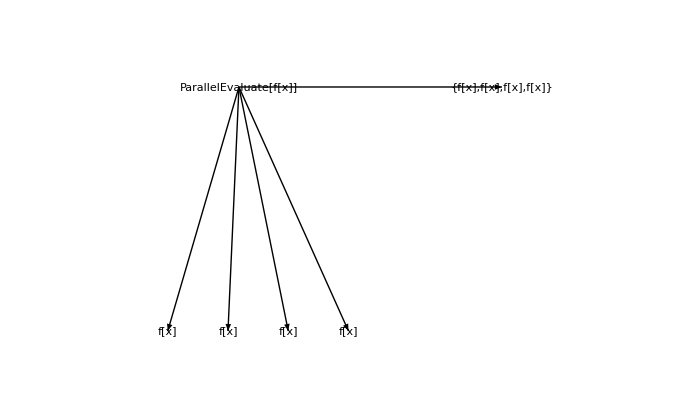

```mathematica
CellPrint[
ExpressionCell[
diagram["ParallelEvaluate[f[x]]",{"f[x]","f[x]","f[x]","f[x]"},"{f[x],f[x],f[x],f[x]}"],
"Output",
GeneratedCell -> False
]
]
```

```mathematica
LaunchKernels[]
```

```mathematica
AbsoluteTiming[Table[Length@FactorInteger[10^50+i], {i, 20}]]
```

```mathematica
AbsoluteTiming[ParallelTable[Length@FactorInteger[10^50+i], {i, 20}]]
```

You can see where it performs the individual computations by labeling them:

```mathematica
AbsoluteTiming[Table[Labeled[Length@FactorInteger[10^50+i], Style[$KernelID, Gray]], {i, 20}]]
```

```mathematica
AbsoluteTiming[ParallelTable[Labeled[Length@FactorInteger[10^50+i], Style[$KernelID, Gray]], {i, 20}]]
```

```mathematica
CloseKernels[]
```

## Code Compilation

### FunctionCompile

Wolfram Language functions are designed to be very general, typically automatically handling real, complex, exact, symbolic and high-precision input automatically. While this is convenient, it comes at a cost to performance.

The Wolfram Language compiler allows you to limit the expectation of inputs to certain types, allowing the compiler to automatically optimize your code.

#### Example: Nested sine

While a real argument, 10.1, is provided to this function, the function does not know that in advance:

```mathematica
nestedSine = Function[{arg,n},Nest[Sin,arg, n]];
```

```mathematica
nestedSine[10.1,5000000]//AbsoluteTiming
```

Indeed, it could have been complex:

```mathematica
nestedSine[10.1+ I,5000000]//AbsoluteTiming
```

However, if you know the expected types, you can annotate the arguments with Typed to convey the expectation. You can then use FunctionCompile to optimize the code:

```mathematica
compiledNestedSine=FunctionCompile[
Function[{Typed[arg,"MachineReal"],Typed[n,"Integer64"]},Nest[Sin,arg, n]]
]
```

```mathematica
compiledNestedSine[10.1, 5000000]//AbsoluteTiming
```

The optimization involves generating LLVM code and then the assembler for the current machine architecture:

```mathematica
FunctionCompileExportString[
Function[{Typed[arg,"MachineReal"],Typed[n,"Integer64"]},Nest[Sin,arg, n]],
"LLVM"
]//CreateDocument;
```

```mathematica
FunctionCompileExportString[
Function[{Typed[arg,"MachineReal"],Typed[n,"Integer64"]},Nest[Sin,arg, n]],
"Assembler",
TargetSystem->"Windows-x86-64"
]//CreateDocument;
```

### Compilation Types

The Typed command supports a range of different types:

```mathematica
CellPrint[
ExpressionCell[
Grid[
{
{"Type", "Description"},
{Style["\"Boolean\"", "CodeText"], "Boolean"},
{Style["\"String\"", "CodeText"], "A string type specifier"},
{Style["\"ComplexReal64\"", "CodeText"], "Complex number with IEEE double-precision real and imaginary parts"},
{Style["\"Integer8\"", "CodeText"], "8-bit signed integer"},
{Style["\"Integer18\"", "CodeText"], "16-bit signed integer"},
{Style["\"Integer32\"", "CodeText"], "32-bit signed integer"},
{Style["\"Integer64\"", "CodeText"], "64-bit signed integer"},
{Style["\"Integer128\"", "CodeText"], "128-bit signed integer"},
{Style["\"MachineInteger\"", "CodeText"], "Machine-sized signed integer"},
{Style["\"Real32\"", "CodeText"], "IEEE single-precision real number"},
{Style["\"Real64\"", "CodeText"], "IEEE double-precision real number"},
{Style["\"UnsignedInteger8\"", "CodeText"], "8-bit unsigned integer"},
{Style["\"UnsignedInteger16\"", "CodeText"], "16-bit unsigned integer"},
{Style["\"UnsignedInteger32\"", "CodeText"], "32-bit unsigned integer"},
{Style["\"UnsignedInteger64\"", "CodeText"], "64-bit unsigned integer"},
{Style["\"UnsignedInteger128\"", "CodeText"], "128-bit unsigned integer"},
{Style["\"UnsignedMachineInteger\"", "CodeText"], "Machine-sized unsigned integer"}
},
BaseStyle -> "Text",
Alignment -> Left,
Background -> {None, {{{GrayLevel[0.95],White}},{1->GrayLevel[0.85]}}},
Spacings -> {2, 1.5},
Frame -> All,
FrameStyle -> Gray
],
"Output",
GeneratedCell -> False
]
]
```

Type | Description
"Boolean" | Boolean
"String" | A string type specifier
"ComplexReal64" | Complex number with IEEE double-precision real and imaginary parts
"Integer8" | 8-bit signed integer
"Integer18" | 16-bit signed integer
"Integer32" | 32-bit signed integer
"Integer64" | 64-bit signed integer
"Integer128" | 128-bit signed integer
"MachineInteger" | Machine-sized signed integer
"Real32" | IEEE single-precision real number
"Real64" | IEEE double-precision real number
"UnsignedInteger8" | 8-bit unsigned integer
"UnsignedInteger16" | 16-bit unsigned integer
"UnsignedInteger32" | 32-bit unsigned integer
"UnsignedInteger64" | 64-bit unsigned integer
"UnsignedInteger128" | 128-bit unsigned integer
"UnsignedMachineInteger" | Machine-sized unsigned integer

#### Example: Higher-dimension types

TypeSpecifier can specify higher-dimension types like lists and matrices of numbers:

```mathematica
Clear[map,compiledMap];

map[arg_]:=Map[#^2&, arg];

compiledMap[arg_]=FunctionCompile[
Function[Typed[arg,TypeSpecifier["PackedArray"]["Real64", 1]],Map[#^2&,arg]]
];
```

```mathematica
map[N@Range[10^5]];//AbsoluteTiming
```

```mathematica
compiledMap[N@Range[10^5]];// AbsoluteTiming
```

#### Example: DataStructure

The compiler understands DataStructure objects:

```mathematica
dn=FunctionCompile[
Function[
{Typed[n,"Integer64"]},
Block[
{queue=CreateDataStructure["Queue"]},
Do[If[Mod[i,3]===0,queue["Pop"],queue["Push",i]],{i,n}];
queue["Pop"]
]
]
];
```

```mathematica
dn[50000]//AbsoluteTiming
```

#### Example: Compilation errors

Watch out for compilation errors, such as unassigned variables and bad types:

```mathematica
boolFunction1 = Function[
{Typed[cond, "Boolean"]},
Module[
{x},
If[cond, x=1];
x
]
];

FunctionCompile[boolFunction1]
```

```mathematica
boolFunction2 = Function[{Typed[x, "Boolean"]},Sin[x]];

FunctionCompile[boolFunction2]
```

## Caching and Memoization

Often you wish to prevent repeated calculations by storing past evaluations. The standard idiom for this is to add definitions to the function as they are computed:

```mathematica
f[x_]:=f[x]=code;
```

For example, this recursive definition for Fibonacci numbers is intrinsically very slow:

```mathematica
Clear[fib];

fib[x_]:=fib[x-1]+fib[x-2];
fib[1]=fib[2]=1;
```

```mathematica
AbsoluteTiming[fib[30]]
```

Changing the definition to remember values makes it fast:

```mathematica
Clear[fib2];

fib2[x_]:=fib2[x]=fib2[x-1]+fib2[x-2];
fib2[1]=fib2[2]=1;
```

```mathematica
AbsoluteTiming[fib2[30]]
```

However, all of these cached values have to be stored somewhere:

```mathematica
DownValues[fib2]
```

If you wish to constrain the time period that cached values are maintained, use Once:

```mathematica
Clear[fib3];

fib3[x_]:=Once[fib3[x-1]+fib3[x-2],PersistenceTime->5];
fib3[1]=fib3[2]=1;
```

```mathematica
AbsoluteTiming[fib3[30]]
```

This time, the values are stored as persistent objects:

```mathematica
PersistentObjects["Hashes/Once/*"]//Short
```

These can be deleted with DeleteObject:

```mathematica
DeleteObject[PersistentObjects["Hashes/Once/*"]]
```

If you wish to constrain the amount of stored values, you can use the data structure "LeastRecentlyUsedCache":

```mathematica
Clear[fib4];

fibCache=CreateDataStructure["LeastRecentlyUsedCache",5];

fib4[x_]:=Block[
{compute,previous =fibCache["Lookup",x]},
If[
!MissingQ[previous],
previous,
(
compute = fib4[x-1]+fib4[x-2];
fibCache["Insert",x->compute];
compute
)
]
];

fib4[1]=fib4[2]=1;
```

```mathematica
AbsoluteTiming[fib4[30]]
```

```mathematica
fibCache["Keys"]
```

## Additional Tips

#### Use pure functions

When you repeatedly apply a function, pure (anonymous) functions are faster:

```mathematica
data=RandomReal[1,{10^7}];

squarePlusOne[x_]:=x^2+1;
```

```mathematica
Map[squarePlusOne,data];//AbsoluteTiming
```

```mathematica
Map[#^2+1&,data];//AbsoluteTiming
```

#### Use stricter pattern matching

This is a conceptually concise way to represent bubble sort. With its loose patterns, the repeated searching and comparing is expensive:

```mathematica
bubbleSort[data_]:=data//.{a___,b_,c_,d___}/;b>c:>{a,c,b,d};

data = RandomReal[1,300];

bubbleSort[data];//AbsoluteTiming
```

This more declarative version of the same algorithm is more complex code but executes much faster:

```mathematica
bubbleSort2[data0_List]:=Block[
{data=data0,changed=True,temp},
While[
TrueQ[changed],
changed=False;
Do[
If[
data[[i]]>data[[i+1]],
(
temp=data[[i]];
data[[i]]=data[[i+1]];
data[[i+1]]=temp;
changed=True
)
],
{i,1,Length[data]-1}
]
];
data
]
```

```mathematica
bubbleSort2[data];//AbsoluteTiming
```

Of course, the built-in Sort (which implements a much more sensible sorting algorithm) is faster still:

```mathematica
Sort[data];//AbsoluteTiming
```

#### Use Sow and Reap

When working with lists, use Sow and Reap instead of Append or Prepend:

```mathematica
AbsoluteTiming[
data = {};
Do[
AppendTo[data, RandomReal[x]],
{x, 0, 10^4}
];
data
]
```

```mathematica
AbsoluteTiming[
Reap[
Do[
Sow[RandomReal[x]],
{x, 0, 10^4}
]
][[2, 1]];
]
```

#### Use Block or With

Use Block or With instead of Module:

```mathematica
AbsoluteTiming[Do[Module[{x = 2.}, 1/x], {10^6}];]
```

```mathematica
AbsoluteTiming[Do[Block[{x = 2.}, 1/x], {10^6}];]
AbsoluteTiming[Do[With[{x = 2.}, 1/x], {10^6}];]
```

## Summary

Use built-in functions (and use fewer functions in general).

Use functional programming to operate on data as a whole; do not loop through indexed data.

Use special data structures.

Parallelize.

Compile code.

Store results with caching or memoization.